# PCR3BP

## Introduction

-Graphics-


In this Notebook i reproduce the algorithm which finds itinerary region in the planar circular restricted three body problem proposed in the book(2006) :
	Dynamical Systems, The Three-Body Problem, And Space Mission Design
		Wang Sang Koon
		Martin W. Lo
		Jerrold E.Marsden
		Shane D. Ross
		
The algorithm is described step by step in chapter 4 : “Construction of Trajectories with Prescribed Itineraries”.

## Description of the problem

The CR3BP is about the motion of a particle(referred to as the “third body”) subject to the gravitational field of two massive bodies(such as the Sun and a planet, or a planet and one of its moons) orbiting each other in circular orbits around the common center of mass.
The masses of these two bodies must be much higher then the mass of the third body(such as a spacecraft or an asteroid or a comet), from which the name “restricted”.
If the motion of the third particle is also restricted to lie in the orbital plane of the two “primaries”(called m1 and m2), then we have the PCR3BP.

Assumptions

The basic assumptions of the PCR3BP are then :

	1 - The particle's mass m must be << m1 and m2 ;
	2 - The two primaries m1 and m2 follow circular orbits around their common c.m.(center of mass) ;
	3 - The motion of the particle must lie in the m1-m2 orbital plane.

Adimensionalization

The first thing to do in order to simplify the equations and the magnitudes of number involved is normalization, i.e. make the system nondimensional :

- the unit of mass is the sum of the two primaries’ masses ;
- the unit of length is the constant distance between the two primaries ;
- the unit of time is such that the orbital period of m1 and m2 about their c.m. is 2π ;

⟹  In this normalized units system we have :

- the universal gravitational constant G is equal to 1 ;
- the mean motion of m1 and m2 is also equal to 1 ;
- the only parameter is the Mass parameter 
			
					μ ≐ m2/(m1+m2)

- the gravitational parameters μ1 and μ2 of m1 and m2 coincides with the masses(beacuse G=1)
- the masses of m1 and m2 becomes , respectively :

	m1=μ1=1-μ        and        m2=μ2=μ
	
- supposing that m1>m2 , we also have that μ ∈ [0,1/2]  ;

The conversion from units of distance,velocity and time in the normalized system(d,s,t) to the dimensionalized system(d’,s’,t’ ) is then :

	distance   d’ = L*d 
	velocity     s’  = V *s
	time         t’ = T/(2π) * t       
	
where L is the distance between m1 and m2 , V is the orbital velocity of m2 and T is the orbital period of m1 and m2.

-Graphics-

Transformation between inertial and rotating frames

Let X-Y-Z be an in inertial frame with origin at the m1-m2 c.m. , with X-Y the orbital plane of the two primaries.
Let x-y-z be a rotating reference frame with the same origin and with :
	- x axis always passing through m1 and m2 , directed toward m2 ;
	- y axis lying in the X-Y plane and perpendicular to x axis ;
	- z axis perpendicular to x-y and so always equal to Z axis .

Let t be the angle between x axis and X axis, teh transformation is the a simple rotation of angle t around z=Z axis :

	(X
Y
Z) = A_t (x
y
z)  with  A_t=(cos t | -sin t | 0
sin t | cos t | 0
0 | 0 | 1)
	
-Graphics-

Because the origin of the xyz frame is the m1-m2 c.m. , in the adimensionalized system, the positions of m1 and m2 in this frame are :

	m1_xyz = (x1 , y1 , z1 ) = ( -μ2 , 0 , 0 ) = ( -μ , 0 , 0 )
	
	m2_xyz = (x2 , y2 , z2 ) = ( μ1 , 0 , 0 ) = (1-μ , 0 , 0 )
	
In fact, the c.m. is at x_g such that x1 * x_g+x2 * x_g = 0 and -μ2 * x_g + μ1 * x_g =  -μ * x_g + (1-μ) * x_g = x_g = 0 

The positions of m1 and m2 in the inertial frame are then(through the rotation matrix A_t ) :

	m1_XYZ = (X1 ,Y1 , Z1 ) = ( -μ2 cos t , -μ2 sin t , 0 ) = ( -μ cos t , -μ sin t , 0 )

	m2_XYZ = (X2 ,Y2 , Z2 ) = ( μ1 cos t , μ1 sin t , 0 ) = ( (1-μ) cos t , (1-μ) sin t , 0 )
	
Finally, the position of m in the inertial frame and in the rotating frame are,respectively :

	m_XYZ = ( X , Y , Z )
	
	m_xyz  = ( z , y , z )
	

	
-Graphics-

Gravitational Potential

The gravitational potential to which the particle is subject, in normalized units, is :

	𝒰 = - μ1/r1 - μ2/r2 - 1/2 μ1 μ2
	
where r1 and r2 are the distances of P form m1 and m2 respectively, given by 

	r1^2 = ( X + μ2 cos (t))^2 + ( Y + μ2 sin t )^2 + Z^2
	
	r2^2 = ( X - μ1 cos (t))^2 + ( Y - μ1 sin t )^2 + Z^2
	
and the constant  1/2 μ1 μ2 is added for convetion and will not affect the equations of motion.

Newtonian approach : Inertial frame

In the inertial frame , the Newtonian equations of motion are :

	X^(..) = - 𝒰_X 
	
	Y^(..) =  - 𝒰_Y 
	
	Z^(..) =  - 𝒰_Z  
	
This is a system of 3 second-order non linear and time dependent differential equations (a non-autonomous system).
By transforming into the variables (x,y,z) the equations of motion in the rotating frame can be obtained.
This is the procedure followed, e.g., in the paragraph 2.12 of Curtis(Orbital mechanics for engeneering students).

-Graphics-

where Ω(equal to 1 in the normalized system) is the mean motion of the m1 and m2 orbits , r1 and r2 are the same as here, r12(equal to 1 in normalized units) is the constant distance between the two primaries , and π1 , π2 correnspond, repectively, to m1/(m1+m2) and m2/(m1+m2) ( they are equal to μ1 and μ2 in normalized units).

Lagrangian approach

The Lagrangian in the rotating frame is :

	L(x , y, ẋ , ẏ ) = 1/2 ( (ẋ - y )^2 + (ẏ (+x))^2 ) - U(x,y)
	
which is time-indipendent, with U(x,y) given by 

	U(x,y) = - μ1/r1 - μ2/r2 - 1/2 μ1 μ2

	r1^2 = ( x + (μ2))^2 +y^2 
	
	r2^2 = ( x + (μ1))^2+y^2 
	
The equation of motions can then be derived through the Euler-Lagrange equations 

	
	d/dt(∂L)/(∂(q̇)^i)- (∂L)/(∂q^i) = 0
	
x''[t]= +x[t]+2 y'[t]-(μ (-1+μ+x[t]))/(((-1+μ+x[t])^2+y[t]^2)^(3/2))-((1-μ) (μ+x[t]))/(((μ+x[t])^2+y[t]^2)^(3/2))

y''[t]=+y[t]-2 x'[t]-(μ y[t])/(((-1+μ+x[t])^2+y[t]^2)^(3/2))-((1-μ) y[t])/(((μ+x[t])^2+y[t]^2)^(3/2))

Energy integral and Jacobi constant

The system is Hamiltonian and indipendent of time, so it has a first integral of motion : the energy , which can be expressed both in term of the Hamiltonian H of the system (function of x,y and the conjugate moments p_x , p_y  ) and in term of kinetic energy 1/2 ((ẋ)^2 + (ẏ)^2 ) plus the so-called 
“effective” or “augmented” potential energy  Ū(x,y) =  - 1/2 (x^2+y^2) + U(x,y) :

	E( x , y , ẋ , ẏ  ) = 1/2 ( (ẋ)^2 + (ẏ)^2  ) + Ū( x , y )

The celestial mechanics and dynamical astronomy communities uses C= - 2E , which is called the “Jacobi integral” :

	C( x , y , ẋ , ẏ ) = - ( (ẋ)^2 + (ẏ)^2 ) - 2 Ū( x , y  )

Energy manifold

In the planar CR3BP , the energy manifold given by setting the energy integral equal to a constant e , is a three-dimensional surface embedded in the four-dimensional phase space ( x , y , ẋ , ẏ ) :

	ℳ(μ,e) = { ( x , y , ẋ , ẏ ) | E( x , y , ẋ , ẏ ) == e }
	
The projection of this surface onto the position space in the rotating frame (x,y) is the region of possible motion for a particle of energy e in the field of two masses with mass parameter μ :

	M(μ,e) = { (x,y) | Ū( x , y) ≤ e }    “ Hill’s region ”
	
The boundary of M(μ,e) is the “zero velocity curve” : the locus of points in which the kinetic energy vanishes :

	1/2 ((ẋ)^2 + (ẏ)^2 ) = e -  Ū( x , y)  = 0
	
so they can be derived through the level curves of the effective potential Ū( x , y) = e .

-Graphics3D-

The three “realms” of motion and the Hill’s region

### The three “realms” of motion

The zero velocity curves separate the “forbidden reame”(in which kinetic energy is negative) from the region in which the motion is allowed(the Hill’s region). For a given μ there are five basic configurations for the Hill’s region, corrensponding to five intervals of energy value , e.

There are three “realms of possible motion” :

	- “Interior realm” or “m1 realm”
	- “m2 realm”
	- “Exterior realm”
	
Depending on the energy of the particle E , these three realms can be connected or not . This can be seen in the following plots .

### Case 1 (E<E1)

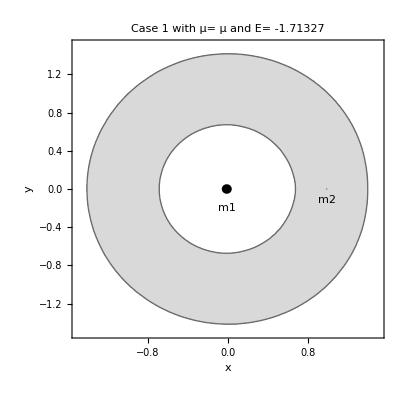

### Case 2 (E1<E<E2)

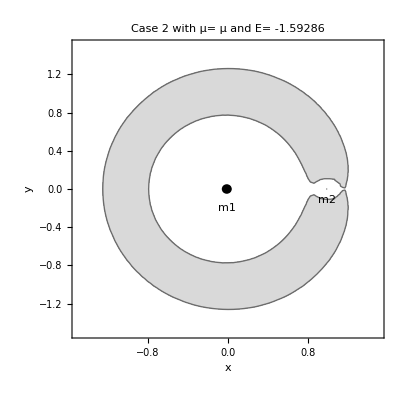

### Case 3 (E2<E<E3)

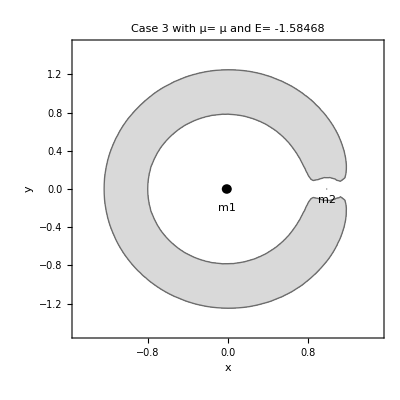

### Case 4 (E3<E<E4)

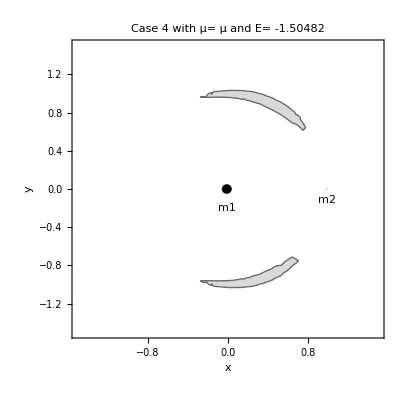

### Case 5 (E>E4)

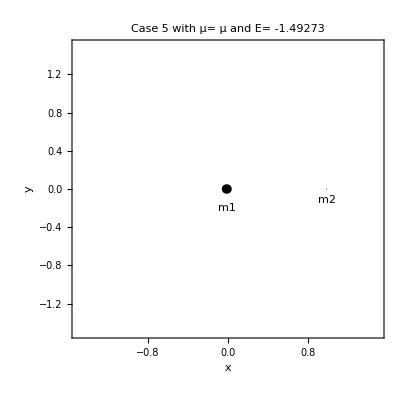

Lagrange points L1,L2,L3,L4,L5

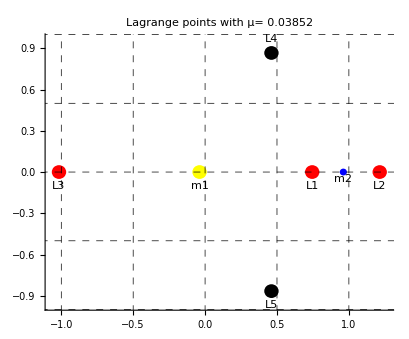
The potential energy surface has five critical points , corrensponding to 5 equilibrium points of the system(in the rotating frame).
These points are known as “Lagrange points” or “Lagrangian points” or “Libration points”.

The previous energy values E1,E2,E3,E4,E5 that distinguished 5 possible cases for the regions in which motion of the particle is possible , are the minimum energies required to reach, respectively, the L1,L2,L3,L4,L5 Lagrange points.
It holds that E5=E4 > E3 > E2 > E1 .

Three of these points are collinear on the x-axis (L1,L2,L3) and the other two are equilateral points( L4 and L5 ).

-Graphics-

Eigenvalues and eigenvectors of the collinear points-linearized system

Working on the linearized system’s state matrix, we find that the eigenvalues are of the form

	±λ  and ± iν 
	
And so there are two modes exponentially stable and unstable respectively, and two complex modes resulting in a periodic oscillation.

The general solution is then

		α1 e^λt u1 + α2 e^-λt u2 + 2 Re(β e^(i ν t)w1 )
	
where α1,α2 and β=β1 + i β2 are constants depending on the initial conditions on x,y,x’,y’ and u1,u2,w1 are the eigenvectors(u1 relative to +λ , u2 relative to -λ , w1 relative to + iν , with w2 equal to the complex conjugate of w1 ).

Geometry of Solutions near the Equilibria

The general solution of the linearized system is

	α1 e^λt u1 + α2 e^-λt u2 + 2 Re(β e^(i ν t)w1 )
	
⟹ te  with α1=α2=0 the solution is periodic with x amplitude A_x = -2*β and transforming back to the original coordinates :

	x_0 = (xe,0,0,0) + 2 Re(β w1) = (xe-A_x ,0 ,0 , vy0)
	
	where vy0= -A_xν τ ( with ν and τ defined above)
	
Caveat : this initial conditions generate a periodic orbit in the linearized system’s phase space, but to find periodic orbits in the original,non linear system , one should search them randomly numerically or , as it is done later, using differential correction and numerical continuation(step 3 of the algorithm).

## Implementation of the Algorithm

Functions

### Function funcPCR3BPeffectivePotentialEnergy

```mathematica
funcPCR3BPeffectivePotentialEnergy[μValue_]:=PCR3BPeffectivePotentialEnergy /. μ->μValue
```

### Function funcHillRegionsPlot

```mathematica
funcHillRegionsPlot[systemId_,e_,directives___]:=Module[{μ,primary,secondary},
μ= SystemsData[systemId,"μ"] ;
primary = SystemsData[systemId,"System"][[1]];
secondary = SystemsData[systemId,"System"][[2]];
Show[{
ContourPlot[funcPCR3BPeffectivePotentialEnergy[μ], {x[t] , -3,3} , {y[t],-3,3} ,
Contours -> {e} ,
ContourShading->{None,LightGray},ColorFunction->"Rainbow" ,
FrameLabel -> { "x" , "y" }
],
Graphics[{
{Black,Disk[{-μ,0},.05]},
{Text[primary,{-μ,-.2}]},
{Black,Disk[{1-μ,0},.005]},
{Text[secondary,{1-μ,-.12}]}
}
]
},
directives
]
]
```

### Function funcSetMinimumEnergy

```mathematica
funcSetMinimumEnergy[systemId_,itinerary_]:=Module[{ 
realms ,minEnergy
},
realms = Union[itinerary] ;
minEnergy =If[
 Length[realms]≥ 2  && MemberQ[itinerary,"X"] ,SystemsData[systemId,"E2"] , 
SystemsData[systemId,"E1"]
]
];
```

### Function funcCheckEnergyLevel

```mathematica
funcCheckEnergyLevel[ systemId_,itinerary_ , energy_ ] :=Module[{minEnergy},
minEnergy=funcSetMinimumEnergy[systemId,itinerary];
If[energy<minEnergy , Print["The energy level must be greater then " , minEnergy ] ,
Print["The energy level is ok for the itinerary " , itinerary ] 
]
];
```

### Function funcL4L5

```mathematica
funcL4L5[μ_] := 
{{1/2-μ, (Sqrt[3]/2)  },{1/2-μ, -(Sqrt[3]/2)  }} //N;
```

### Function funcL1L2L3

```mathematica
funcL1L2L3[μ_] :=Module[{sol,L1,L2,L3},
sol=NSolve[ (1-μ)/Abs[ξ+μ]^3 (ξ+μ) + μ/Abs[ξ+μ-1]^3 (ξ+μ-1) -ξ==0 , ξ  , Reals] ;
L1 = { sol[[2,1,2]] ,0  } ;
L3 = {sol[[1,1,2]],0  } ;
L2 = {sol[[3,1,2]],0} ;
{L1,L2,L3}
];
```

### Function funcLagrangePoints

```mathematica
funcLagrangePoints[μ_]:=Module[ {L45 , L123 } ,
L45 = funcL4L5[μ];
L123=funcL1L2L3[μ];
Join[L123,L45]
] ;
```

### Function funcLagrangePointsPlot

```mathematica
funcLagrangePointsPlot[systemId_]:=
Module[ {μ,primary,secondary,Lpoints},
μ= SystemsData[systemId,"μ"] ;
primary = SystemsData[systemId,"System"][[1]];
secondary = SystemsData[systemId,"System"][[2]];
Lpoints =NumberForm[funcLagrangePoints[μ],16];
 Show[{
Graphics[{
{ Yellow , Disk[{-μ,0},.05] } ,
{Text[primary,{-μ,-.1}]},

{ Blue , Disk[{1-μ,0},.025] } ,
{Text[secondary,{1-μ,+.05}]},

{ Red , Disk[Lpoints[[1,#]],.02 ] & /@ Range[1,3] },
{ Text["L1",Lpoints[[1,1]]-{0,.1}] },
{ Text["L2",Lpoints[[1,2]]-{0,.1}] },
{ Text["L3",Lpoints[[1,3]]-{0,.1}] },

{ Black , Disk[Lpoints[[1,#]],.02] & /@ Range[4,5] },
{ Text["L4",Lpoints[[1,4]]+{0,.1}] },
{ Text["L5",Lpoints[[1,5]]-{0,.1}] }

}]
},
ImageSize -> Large ,
GridLines->{Range[-2,2,.5],Range[-2,2,.5]},
GridLinesStyle->Directive[Black,Dashed],
Axes->True,AxesStyle->Thick ,
PlotLabel->Style[Framed["Lagrange points of = " <> ToString[primary]<>"-"<>ToString[secondary]<> " system"],16,Blue,Background->Lighter[Green]],
AxesLabel->{"x(rotating frame)","y(rotating frame)"}
]
];
```

### Function funcPCR3BPnonLinEqns

```mathematica
funcPCR3BPnonLinEqns[x0_,t0_]:={
PCR3BPeqnsOfMotion[[1]]==0,PCR3BPeqnsOfMotion[[2]]==0 ,
 x[t0]==x0[[1]], y[t0]==x0[[2]],x'[t0]==x0[[3]]  , y'[t0]==x0[[4]]
}
```

### Function funcPCR3BPlinearization

```mathematica
funcPCR3BPlinearization[xeq_]:=Module[ {TwoOrdEq1 , TwoOrdEq2 , firstOrdSystem } ,
TwoOrdEq1=Solve[PCR3BPeqnsOfMotion[[1]]==0,x''[t]];
TwoOrdEq2=Solve[PCR3BPeqnsOfMotion[[2]]==0,y''[t]];
firstOrdSystem = {
x'[t]    == vx[t] ,
y'[t]    == vy[t] ,
vx'[t] == TwoOrdEq1[[1,1,2]]/. {x'[t]-> vx[t] , y'[t] -> vy[t] },
vy'[t] == TwoOrdEq2[[1,1,2]]/. {x'[t]-> vx[t] , y'[t] -> vy[t] }
} ;
StateSpaceModel[firstOrdSystem ,
 {{ x[t] , xeq[[1]]},{y[t],xeq[[2]]},{vx[t],xeq[[3]]},{vy[t],xeq[[4]]}},{{nullInput[t],0}},{},t]
]
```

### Function funcLinStateSol

```mathematica
funcLinStateSol[α1_,α2_,β1_,β2_]:= 
α1 e^λt u1 + α2 e^-λt u2 + 2 Re[((β1+ I β2) e^(i ν t)w1 )] ;
```

### Function funcSetLpoint

```mathematica
funcSetLpoint[μ_,lagrPointName_]:=Module[{lagPoints, L1 , L2 , L3,L4,L5, L1Rule , L2Rule , L3Rule, L4Rule, L5Rule },
lagPoints=funcLagrangePoints[μ];
{ L1 , L2 , L3,L4,L5 }= lagPoints  ;
{ L1Rule , L2Rule , L3Rule, L4Rule, L5Rule  }  =  {xe->L1[[1]] , xe->L2[[1]] , xe->L3[[1]] ,  {xe->L4[[1]],ye->L4[[2]]} ,  {xe->L4[[1]],ye->-L4[[2]]} } ;

Switch[ lagrPointName ,
"L1" , { L1Rule ,  L1JS },
"L2" , { L2Rule ,  L2JS } ,
"L3" , { L3Rule ,  L3JS } ,
"L4", { L4Rule ,  L4JS },
"L5", { L5Rule ,  L5JS }
] 

]
```

### Function funcLinSysStateResponse

```mathematica
funcLinSysStateResponse[systemId_,lagrPointName_,x0_,t0_,tfin_]:=
Module[{μf,Lrule},
μf = SystemsData[systemId,"μ"] ;
Lrule=funcSetLpoint[μf,lagrPointName][[1]];
StateResponse[ {PCR3BPlinearizedSystemCollinearLagrangePoints/.{μ->μf, Lrule }  , x0} ,  0 , {t,t0,tfin}] 
]
```

### Function funcOrbitEnergy

```mathematica
funcOrbitEnergy[μf_,x0_]:=PCR3BPenergy /. {μ->μf,x[t]-> x0[[1]] , y[t]-> x0[[2]],x'[t]-> x0[[3]],y'[t]-> x0[[4]] } ;
```

### Function funcInCondLyapOrbit

```mathematica
funcInCondLyapOrbit[μf_,collinearLagrangePoint_,xAmpl_]:={-xAmpl , 0 , 0 , -xAmpl*ν*τ } /.{μ-> μf , funcSetLpoint[μf,collinearLagrangePoint][[1]]} ;
```

### Function funcNLpoX0Guess

```mathematica
funcNLpoX0Guess[μ_,collinearLagrangePoint_,Ax_]:= Module[{Lpoint,Lpo },
Lpoint = funcSetLpoint[μ,collinearLagrangePoint][[2]];
Lpo = funcInCondLyapOrbit[μ,collinearLagrangePoint,Ax];
{ Lpoint[[1]]+ Lpo[[1]],0,0 , Lpo[[4]] } 
] ;
```

### Function funcIntegratePCR3BP

```mathematica
funcIntegratePCR3BP[ μf_ ,x0_ , tin_ , tfin_,method___ ] :=
Module[ { solRules },
solRules=Flatten[NDSolve[
funcPCR3BPnonLinEqns[x0,tin]/.μ-> μf   ,
{x,y,x',y'},
{t,tin,tfin},
method
]]   ;
solRules[[All,2]] 
]  ;
```

### Function funcNonLinSystemPlot

```mathematica
funcNonLinSystemPlot[ μf_,x0_ , tin_ , tfin_,directives___ ] :=
Module[ { resp},
resp =funcIntegratePCR3BP[ μf,x0 , tin , tfin] ;
ParametricPlot[ Evaluate[{ resp[[1]][t],resp[[2]][t]} ] , {t,tin,tfin} ,
directives ] 
];
```

### Function funcPCR3BPFlowJacobian

```mathematica
funcPCR3BPFlowJacobian[μf_,traj_]:=
Module[{Jacobian,JacobianOnTrajectory},
Jacobian=D[PCR3BPnonLinearFlow /.μ-> μf , { {x[t],y[t],x'[t],y'[t]} } ]  ;
JacobianOnTrajectory=Jacobian /. { x[t]->  traj[[1]][t] , y[t]->  traj[[2]][t] } 
];
```

### Function funcPCR3BPvariationalEqns

```mathematica
funcPCR3BPvariationalEqns[μf_,traj_]:=Module[{Φ,Jtraj},
Φ=PCR3BPtransitionMat ;
Jtraj = funcPCR3BPFlowJacobian[μf,traj] ;
MapThread[{ 
D[Φ[[#1,#2]],t]== Jtraj[[#1,All]].Φ[[All,#2]] , ( Φ[[#1,#2]]/. t->0)== KroneckerDelta[#1,#2]
 } &,
{
{1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4},
{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}
 }]
];
```

### Function funcPCR3BPtransMatrixComputation

```mathematica
funcPCR3BPtransMatCompute[μf_,traj_,t0_,tfin_,tEv_]:=
 (* Compute state transition matrix Φ from PCR3BP variational equations 
solving them around solution traj from t0 to tfin , and evaluate it at time tEv *)
Module [ {ΦEqns ,Φsol,Φ,ΦtEv } ,
ΦEqns =funcPCR3BPvariationalEqns[μf,traj] ;
Φsol=NDSolve[  ΦEqns , Flatten[PCR3BPtransitionMat],{t,t0,tfin} ]  ;
Φ= First[ PCR3BPtransitionMat /. Φsol  ] ;
ΦtEv = Φ/.t-> tEv 
];
```

### Function funcDifferentialCorrection

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
funcDifferentialCorrection[μf_, x0g_ ,tfin_, d_ ] :=
Module [ { k=1,
trajTillIntersection, x1 , y1 , x1Dot , y1Dot,t1 ,xt1 ,TransMatInt1 ,δvy0 ,x0New ,x0 , vx
} ,
x0 = x0g ;
vx=10 ;

Do[
k=k+1;
If[Abs[vx]<d,Break[],Unevaluated[Sequence[]]] ;

trajTillIntersection= funcIntegratePCR3BP[μf,x0, 0 , tfin ,Method-> {"EventLocator","Event"-> y[t] }] ;
{ x1 , y1 , x1Dot , y1Dot } = trajTillIntersection[[All]] ;
         t1 = InterpolatingFunctionDomain[y1][[1,-1]] ;
         xt1 = trajTillIntersection[[#]][t1] & /@ Range[1,4]  ;
vx= xt1[[3]];
TransMatInt1 =funcPCR3BPtransMatCompute[μf,trajTillIntersection,0,t1,t1] ;

(* DIFFERENTIAL CORRECTION *)
δvy0 = ( TransMatInt1[[3,4]]-(1/xt1[[4]]) TransMatInt1[[2,4]])^-1 * xt1[[3]] ;
x0New = { x0[[1]] , x0[[2]] , x0[[3]] , x0[[4]]+δvy0 } ;
          x0=x0New  ,
{k,∞}
] ;

{t1,x0 , xt1 }

] ;
```

### Function funcComputeLyapOrb

```mathematica
funcComputeLyapOrb[μf_,collinearLagrangePoint_,Ax_,tfin_,d_]:=Module[ { x0g },

x0g= funcNLpoX0Guess[μf,collinearLagrangePoint,Ax] ;

funcDifferentialCorrection[μf, x0g, tfin,d]

];
```

### Function funcNumericalContinuation

```mathematica
funcNumericalContinuation[μf_,{x1g_,t11_},{x2g_,t12_},tfin_, d_]:=
Module[{x01,x02,Δ,x03g,t13,x03,x13 , x0dummy  } ,

x01=x1g ;
x02 =x2g ;

Δ = x2g-x1g  ;

x03g = x2g+Δ  ;

{t13,x03,x13}=funcDifferentialCorrection[μf,x03g ,tfin, d ]  ;

{ x03 , t13 }
] ;
```

### Function funcGenerateLyapunovOrbitFamily

```mathematica
funcGenerateLyapunovOrbitFamily[μf_,lagrPointName_ ,inAx_,tfin_,d_, n_]:=Module[{
t11,t12,t13,x01,x02,x03,x11,x12,x0List,t1List,Δ
},

{t11 ,x01 , x11 } =  funcComputeLyapOrb[μf,lagrPointName,inAx            ,tfin,d]  ;
{t12 ,x02 , x12 } =  funcComputeLyapOrb[μf,lagrPointName,1.05*inAx,tfin,d]  ;

x0List = ConstantArray[0,{Max[n,3],4}] ;
t1List =  ConstantArray[0,Max[n,3]] ;

x0List[[1]]=x01 ;
x0List[[2]]=x02 ;

t1List[[1]] = t11  ;
t1List[[2]] = t12 ;

Do[
{x03,t13}=funcNumericalContinuation[μf,{x01,t11},{x02,t12},tfin, d] ;
x0List[[k]]=x03;
t1List[[k]]=t13;

x01 =x02 ;
t11 = t12 ;

x02 = x03 ;
t12 = t13 ,

{k,3,Max[3,n],1}
];
{x0List[[1;;n]],t1List[[1;;n]]}
] ;
```

### Function funcFindFirstPossibleX0andt1Values

```mathematica
funcFindFirstPossibleX0andt1Values[μf_,e_,x0List_,t1List_,lagrPointName_:"L1",inAx_:10^-3,tfin_:8,d_:10^-7]:=
Module[{Xlist,Tlist,energies,test, x0 , t1 , numbOfOrbs ,x01,t11 ,x02,t12, x0new,t1new },
Xlist=x0List ;
Tlist = t1List ;
numbOfOrbs = Length[Xlist] ;
energies=funcOrbitEnergy[μf,Xlist[[#]]]&/@ Range[1,numbOfOrbs];
test=energies[[#]]≥e & /@ Range[1,numbOfOrbs];

If[ MemberQ[test,True]==False ,
{
If[numbOfOrbs<2 ,
{
{x01,t11} = {Xlist[[1]],Tlist[[1]]};
{x02,t12} =  funcComputeLyapOrb[μf,lagrPointName,1.05*inAx,tfin,d] [[1;;2]]
},
{
{x01,t11} = {Xlist[[-2]],Tlist[[-2]]};
{x02,t12} = {Xlist[[-1]],Tlist[[-1]]}
}
];

Do[

{x0new,t1new}=funcNumericalContinuation[μf,{x01,t11},{x02,t12},tfin, d] ;
Xlist=Append[Xlist,x0new];
Tlist=Append[Tlist,t1new] ;

energies=funcOrbitEnergy[μf,Xlist[[#]]]&/@ Range[1,Length[Xlist]];
test=energies[[#]]≥e & /@ Range[1,Length[Xlist]];

If[MemberQ[test,True]==True ,
Break[] ,
{
{x01,t11} = {Xlist[[-2]],Tlist[[-2]]};
{x02,t12} = {Xlist[[-1]],Tlist[[-1]]}
}
],

{k,∞}
]
},
 Unevaluated[Sequence[]]
 ] ;

x0= Xlist[[FirstPosition[test,True]]][[1]] ;
t1= Tlist[[FirstPosition[test,True]]][[1]] ;

{x0,t1}
];
```

### Function funcMonodromyMatrix

```mathematica
funcMonodromyMatrix[μf_,x0_,t1_]:=  (* x0 initial condition for the desired p.o. with half period equal to t1 *)
Module [ { traj} ,
traj = funcIntegratePCR3BP[μf ,x0 , 0 , 2*t1] ;
funcPCR3BPtransMatCompute[μf,traj,0,2*t1,2*t1]
];
```

### Function funcLinspace

```mathematica
funcLinspace[start_,stop_,n_:100]:=If[n≠ 1 ,Table[x,{x,start,stop,(stop-start)/(n-1)}] , {start} ] ;
```

### Function funcComputeInvManifoldDirections

```mathematica
funcComputeInvManifoldDirections[μf_,x0_,t1_]:=
Module[{
M,FloquetMultipliers,oneEig,stableAndUnstEig,λUnstable,λStable,Yunstable,Ystable,ϵ,XstablePlus,XstableMinus,XunstablePlus,XunstableMinus
},
M=funcMonodromyMatrix[μf,x0,t1] ;
FloquetMultipliers=Eigenvalues[M] ;
oneEig=Flatten[Position[Im[FloquetMultipliers[[#]]]&/@Range[1,4] ,_?(#≠0&)]] ; 
stableAndUnstEig = FloquetMultipliers[[Drop[Range[1,4],oneEig]]] ;
λUnstable=Re[stableAndUnstEig[[Flatten[Position[Re[stableAndUnstEig [[#]]]&/@Range[1,2] ,_?(#>1&)]]]]][[1]] ;
λStable=Re[stableAndUnstEig[[Flatten[Position[Re[stableAndUnstEig [[#]]]&/@Range[1,2] ,_?(#<1&)]]]]][[1]];
Yunstable =Normalize[ Re[Eigenvectors[ M ][[1]][[#]] & /@ Range[1,4] ] ];
Ystable  =Normalize[ Re[Eigenvectors[ M ][[4]][[#]] & /@ Range[1,4] ] ];
ϵ = 10^-6 ;
XstablePlus = x0 + ϵ Ystable;
XstableMinus = x0 - ϵ Ystable;
XunstablePlus = x0 + ϵ Yunstable;
XunstableMinus = x0 - ϵ Yunstable;

{XstablePlus,XstableMinus ,XunstablePlus ,XunstableMinus} 
];
```

### Function funcSetManifoldPoincareSections

```mathematica
funcSetManifoldPoincareSections[lagrPointName_]:=Module[{
stablePlusSection,stableMinusSection,unstablePlusSection,unstableMinusSection
 },

stablePlusSection   = If[lagrPointName=="L1" ,  "U1" , "U4" ] ;
stableMinusSection = If[lagrPointName=="L1" ,  "U3" , "U2" ] ;

unstablePlusSection   = If[lagrPointName=="L1" ,  "U2" , "U4" ] ;
unstableMinusSection =If[lagrPointName=="L1" ,  "U1" , "U3" ] ;

{stablePlusSection,stableMinusSection,unstablePlusSection,unstableMinusSection }
]
```

### Function funcSetPoincareSection

```mathematica
funcSetNDSolveMethodForPoincareSection[μf_,sectionName_]:=Switch[sectionName,

"U1",{"EventLocator","Event"-> y[t] , "EventCondition"->(x[t]< 0 ) ,
 "EventAction":>Sow[{{x[t],y[t],x'[t],y'[t]},t}] } , (* && x[t] > -1) }, *)

"U2",{"EventLocator","Event"-> x[t] -(1-μf), "EventCondition"->(y[t]< 0)  ,
 "EventAction":>Sow[{{x[t],y[t],x'[t],y'[t]},t}]}  , (* && y[t]>-0.2 ) }, *)

"U3",{"EventLocator","Event"-> x[t] -(1-μf) , "EventCondition"->(y[t]> 0 ) ,
 "EventAction":>Sow[{{x[t],y[t],x'[t],y'[t]},t}]}, (* && y[t]<0.2) }, *)

"U4",{"EventLocator","Event"-> y[t] , "EventCondition"->(x[t]< 0 )  ,
 "EventAction":>Sow[{{x[t],y[t],x'[t],y'[t]},t}]} (* && x[t]<-1) } *)

]
```

### Function funcComputeTrajTillPoincareSection

```mathematica
funcComputeTrajTillPoincareSection[μf_,x0_,tin_,tfin_,sectionName_]:=Module[{
PoincareSection,trajTillIntersection,intersectionTime , solAndIntersections ,intersectionPoints, intersectionTimes
},
PoincareSection=funcSetNDSolveMethodForPoincareSection[μf,sectionName];

solAndIntersections=Reap[
NDSolve[
funcPCR3BPnonLinEqns[x0,tin]/.μ-> μf   ,
{x,y,x',y'},
{t,tin,tfin},
Method->PoincareSection
]
] ;

If[solAndIntersections[[2]]≠ {}, 
{
trajTillIntersection = solAndIntersections[[1,1]] ;
     intersectionPoints = solAndIntersections[[2,1,All,1]] ;
intersectionTimes = solAndIntersections[[2,1,All,2]] ;
{ trajTillIntersection , intersectionPoints , intersectionTimes }
},
Unevaluated[Sequence[]]
]



(*

trajTillIntersection =funcIntegratePCR3BP[μf,x0,tin,tfin, Method-> PoincareSection] ;

  intersectionTime=If[tfin<0 , 
InterpolatingFunctionDomain[trajTillIntersection[[1]]] [[1,1]],
InterpolatingFunctionDomain[trajTillIntersection[[1]]][[1,-1]] 
] ;

      If[intersectionTime≠ tfin ,{ trajTillIntersection , intersectionTime } , Unevaluated[Sequence[]]]
*)
]
```

### Function funcComputeLyapunovOrbitInvariantManifolds

```mathematica
funcComputeLyapunovOrbitInvariantManifolds[μf_,lagrPointName_,x0_, t1_,τPlus_,τMinus_,granularity_:100]:=
Module[{ 
ϵ ,Ystables,Yunstables , periodicOrbit , TransMatInAperiod,M , YstableX0 , YunstableX0 ,
 XstablesPlus , XstablesMinus , XunstablesPlus , XunstablesMinus ,PoincareSections,
StablePlusManifoldAndTimes,StableMinusManifoldAndTimes,UnStablePlusManifoldAndTimes,UnStableMinusManifoldAndTimes,
Xti , times ,StableManifoldPlus,StableManifoldMinus,UnStableManifoldPlus,UnStableManifoldMinus ,
StablePlusFinalTimes , StableMinusFinalTimes ,UnStablePlusFinalTimes ,UnStableMinusFinalTimes , FinalTimes,
StablePlusTrajAndIntersect , StableMinusTrajAndIntersect , UnStablePlusTrajAndIntersect ,  UnStableMinusTrajAndIntersect ,
StablePlusIntersectPoints , StableMinusIntersectPoints  ,  UnStablePlusIntersectPoints ,  UnStableMinusIntersectPoints ,
 StablePlusIntersectTimes  ,  StableMinusIntersectTimes ,UnStablePlusIntersectTimes   ,UnStableMinusIntersectTimes  , 
IntersectPoints , IntersectTimes ,
InvariantManifolds  
},
ϵ = 10^-6 ;

periodicOrbit= funcIntegratePCR3BP[μf,x0, 0 , 2*t1 ] ;
M =funcMonodromyMatrix[μf,x0,t1] ;

YstableX0  =Normalize[ Re[Eigenvectors[ M ][[4]][[#]] & /@ Range[1,4] ] ] ;
YunstableX0  =Normalize[ Re[Eigenvectors[ M ][[1]][[#]] & /@ Range[1,4] ] ] ;

times = funcLinspace[0,2*t1,granularity] ;

TransMatInAperiod=funcPCR3BPtransMatCompute[μf,periodicOrbit,0,2*t1,t]/.t->times[[#]]&/@Range[1,granularity] ;

Ystables = Normalize[(TransMatInAperiod.YstableX0)[[#]] ]&/@Range[1,granularity]  ;
Yunstables = Normalize[ (TransMatInAperiod.YunstableX0)[[#]] ]&/@Range[1,granularity] ;

Xti = Transpose[periodicOrbit[[#]][times]&/@Range[1,4] ] ;

XstablesPlus =Xti[[#]]+ ϵ Ystables[[#]]&/@Range[1,granularity] ;
XstablesMinus =Xti[[#]]- ϵ Ystables[[#]]&/@Range[1,granularity] ;

XunstablesPlus =Xti[[#]]+ϵ Yunstables[[#]]&/@Range[1,granularity] ;
XunstablesMinus =Xti[[#]]-ϵ Yunstables[[#]]&/@Range[1,granularity] ;

PoincareSections = funcSetManifoldPoincareSections[lagrPointName] ;

(* Positive branch of the stable Manifold *)
StablePlusTrajAndIntersect=funcComputeTrajTillPoincareSection[μf,XstablesPlus[[#]],0,-τPlus ,PoincareSections[[1]]]&/@Range[1,granularity]  ;
StableManifoldPlus =  StablePlusTrajAndIntersect[[All,1,1]];
StablePlusIntersectPoints= StablePlusTrajAndIntersect[[All,1,2]] ;
StablePlusIntersectTimes= StablePlusTrajAndIntersect[[All,1,3]] ;


(* Negative branch of the stable Manifold *)
StableMinusTrajAndIntersect=funcComputeTrajTillPoincareSection[μf,XstablesMinus[[#]],0,-τMinus ,PoincareSections[[2]]]&/@Range[1,granularity]  ;
StableManifoldMinus =  StableMinusTrajAndIntersect[[All,1,1]];
StableMinusIntersectPoints= StableMinusTrajAndIntersect[[All,1,2]] ;
StableMinusIntersectTimes= StableMinusTrajAndIntersect[[All,1,3]] ;

(* Positive branch of the unstable Manifold *)
UnStablePlusTrajAndIntersect=funcComputeTrajTillPoincareSection[μf,XunstablesPlus[[#]],0,τPlus ,PoincareSections[[3]]]&/@Range[1,granularity]  ;
UnStableManifoldPlus =  UnStablePlusTrajAndIntersect[[All,1,1]];
UnStablePlusIntersectPoints=UnStablePlusTrajAndIntersect[[All,1,2]] ;
UnStablePlusIntersectTimes= UnStablePlusTrajAndIntersect[[All,1,3]] ;

(* Negative branch of the unstable Manifold *)
UnStableMinusTrajAndIntersect=funcComputeTrajTillPoincareSection[μf,XunstablesMinus[[#]],0,τMinus ,PoincareSections[[4]]]&/@Range[1,granularity]  ;
UnStableManifoldMinus =  UnStableMinusTrajAndIntersect[[All,1,1]];
UnStableMinusIntersectPoints= UnStableMinusTrajAndIntersect[[All,1,2]] ;
UnStableMinusIntersectTimes= UnStableMinusTrajAndIntersect[[All,1,3]] ;

InvariantManifolds={ StableManifoldPlus , StableManifoldMinus , UnStableManifoldPlus , UnStableManifoldMinus } ;
IntersectPoints = {StablePlusIntersectPoints,StableMinusIntersectPoints ,UnStablePlusIntersectPoints ,UnStableMinusIntersectPoints  } ;
IntersectTimes = {StablePlusIntersectTimes ,StableMinusIntersectTimes ,UnStablePlusIntersectTimes ,UnStableMinusIntersectTimes } ;


{InvariantManifolds ,IntersectPoints ,  IntersectTimes}

(*
(* Positive branch of the stable Manifold *)
StablePlusManifoldAndTimes = funcComputeTrajTillPoincareSection[μf,XstablesPlus[[#]],
0,-τPlus ,PoincareSections[[1]] ]&/@Range[1,granularity]  ;
StableManifoldPlus = StablePlusManifoldAndTimes[[All,1]];
StablePlusFinalTimes  = StablePlusManifoldAndTimes[[All,2]];

(* Negative branch of the stable Manifold *)
StableMinusManifoldAndTimes = funcComputeTrajTillPoincareSection[μf,XstablesMinus[[#]],
0,-τMinus ,PoincareSections[[2]] ]&/@Range[1,granularity]  ;
StableManifoldMinus = StableMinusManifoldAndTimes[[All,1]];
StableMinusFinalTimes  = StableMinusManifoldAndTimes[[All,2]];

(* Positive branch of the unstable Manifold *)
UnStablePlusManifoldAndTimes = funcComputeTrajTillPoincareSection[μf,XunstablesPlus[[#]],
0,τPlus ,PoincareSections[[3]] ]&/@Range[1,granularity]  ;
UnStableManifoldPlus = UnStablePlusManifoldAndTimes[[All,1]];
UnStablePlusFinalTimes  = UnStablePlusManifoldAndTimes[[All,2]];

(* Negative branch of the unstable Manifold *)
UnStableMinusManifoldAndTimes = funcComputeTrajTillPoincareSection[μf,XunstablesMinus[[#]],
0,τMinus ,PoincareSections[[4]] ]&/@Range[1,granularity]  ;
UnStableManifoldMinus = UnStableMinusManifoldAndTimes[[All,1]];
UnStableMinusFinalTimes  = UnStableMinusManifoldAndTimes[[All,2]];

InvariantManifolds={ StableManifoldPlus , StableManifoldMinus , UnStableManifoldPlus , UnStableManifoldMinus } ;
FinalTimes = {StablePlusFinalTimes , StableMinusFinalTimes ,UnStablePlusFinalTimes ,UnStableMinusFinalTimes   } ;

{InvariantManifolds , FinalTimes}
*)
];
```

Initialization

```mathematica
SystemsData= Dataset[{
<|"Id"-> 1 , "System"->{"Sun" ,"Jupiter"  }            ,"μ"-> 9.357*10^-4 ,"L"->7.784*10^8 ,"V"->13.102 ,"T"->3.733*10^8,"E1"->-1.5193796428035, "E2"->-1.518743639093 ,"E3" -> -1.5004768982715 , "E4" ->  -1.124523547048 |>,

<|"Id"-> 2 ,"System"->{"Sun" ,"Earth"  }                  ,"μ"-> 3.036*10^-6 ,"L"->1.496*10^8,"V"->29.784 ,"T"->3.147*10^7|>,

<|"Id"-> 3 ,"System"->{"Earth" ,"Moon"  }                ,"μ"-> 1.215*10^-2 , "L"->3.850*10^5,"V"->1.025  , "T"->2.361*10^6|>,

<|"Id"-> 4 ,"System"->{"Mars" ,"Phobos"  }             ,"μ"-> 1.667*10^-8, "L"->9.380*10^3,"V"->2.144   , "T"->2.749*10^4|>,

<|"Id"-> 5 ,"System"->{"Jupiter" ,"Io"  }                ,"μ"-> 4.704*10^-8, "L"->4.218*10^5,"V"->17.390 ,"T"->1.524*10^5|>,

<|"Id"-> 6 ,"System"->{"Jupiter" ,"Europa"  }       ,"μ"-> 2.528*10^-5 , "L"->6.711*10^5,"V"->13.780 ,"T"->3.060*10^5|>,

<|"Id"-> 7 ,"System"->{"Jupiter" ,"Ganymede"  }  ,"μ"->7.804*10^-5 ,  "L"->1.070*10^6,"V"->10.909 ,"T"->6.165*10^5|>,

<|"Id"-> 8 ,"System"->{"Jupiter" ,"Callisto"  }  ,"μ"->5.667*10^-5 , "L"->1.883*10^6, "V"->8.226    ,"T"->1.438*10^6|>

}];

μ1= 1-μ   ;
μ2 = μ ;

r1= Sqrt[ (x[t]+μ2)^2  + y[t]^2  ] ;
r2= Sqrt[(x[t]-μ1)^2  + y[t]^2  ] ;

PCR3BPpotentialEnergy= -μ1/r1 - μ2/r2 - 1/2 μ1 μ2;

PCR3BPlagrangian = (1/2)( (x'[t]-y[t] )^2+(y'[t]+x[t])^2  )-PCR3BPpotentialEnergy;

PCR3BPeqnsOfMotion = D[ D[PCR3BPlagrangian,{{x'[t],y'[t]}}] , t ] - D[PCR3BPlagrangian , {{x[t],y[t]}}] ;

PCR3BPkineticEnergy = 1/2 ( (x'[t] )^2+(y'[t])^2  );
PCR3BPeffectivePotentialEnergy= PCR3BPpotentialEnergy - 1/2 (x[t]^2 + y[t]^2 );

PCR3BPenergy = PCR3BPkineticEnergy + PCR3BPeffectivePotentialEnergy;

PCR3BPjacobiConstant = -2 PCR3BPenergy //Simplify;

(**********************************************************)
PCR3BPnonLinearFlow = Module[ {TwoOrdEq1 , TwoOrdEq2 , firstOrdSystem } ,
TwoOrdEq1=Solve[PCR3BPeqnsOfMotion[[1]]==0,x''[t]];
TwoOrdEq2=Solve[PCR3BPeqnsOfMotion[[2]]==0,y''[t]];
firstOrdSystem = {
x'[t]    ,
y'[t]   ,
TwoOrdEq1[[1,1,2]],
TwoOrdEq2[[1,1,2]]
}
];

PCR3BPlinearizedSystemCollinearLagrangePoints  = funcPCR3BPlinearization[{xe,0,0,0}];

PCR3BPlinStateMatCollinearLagrangePoints = First[Normal[PCR3BPlinearizedSystemCollinearLagrangePoints ]]  ;
Acollinear = PCR3BPlinStateMatCollinearLagrangePoints;
Acollinear//MatrixForm;

a = Acollinear[[3,1]] ;
b = -Acollinear[[4,2]] ;

(**********************************************************)
PCR3BPlinearizedSystemEquilateralLagrangePoints  = funcPCR3BPlinearization[{xe,ye,0,0}] ;

PCR3BPlinStateMatEquilateralLagrangePoints = First[Normal[PCR3BPlinearizedSystemEquilateralLagrangePoints ]]  ;
Aequilateral = PCR3BPlinStateMatEquilateralLagrangePoints;
Aequilateral//MatrixForm;


μs= μ (Abs[xe-1+μ])^(-3) + (1-μ) (Abs[xe+μ])^(-3) ;
Acollinear = Acollinear /. { Acollinear[[3,1]]-> 2 μs+ 1 ,Acollinear[[4,2]]->1-μs}  ;

caracteristicPoly=Det[ β IdentityMatrix[4] - Acollinear ] //Simplify ;

caracteristicPoly=caracteristicPoly /. {β^2-> α , β^4-> α^2 } ;

α1α2=Module[{sol},sol=Solve[caracteristicPoly==0 , α ] ; {sol[[1,1,2]],sol[[2,1,2]]}]  ;

a1 = 1/2 (-2+μs+√μs √(-8+9μs))  ;
a2 = 1/2 (-2+μs-√μs √(-8+9 μs)) ;

λ = Sqrt[a1]  ;
ν = Sqrt[-a2] ;

eig = { λ , -λ , I ν , -I ν }  ;

σ = (2 λ)/(λ^2 + b) ;

τ =- (ν^2+a)/(2 ν) ;

u1 = {1,-σ,λ,-λ σ} ;
u2 = {1,σ,-λ,-λ σ} ;
w1  = {1, -I τ, I ν, ν τ} ;
w2 = {1, I τ, -I ν, ν τ} ;

eigVect = {u1,u2,w1,w2} ;


(************************************************************)
PCR3BPtransitionMat= {
    { Φ11[t] , Φ12[t] , Φ13[t] , Φ14[t] },
    { Φ21[t] , Φ22[t] , Φ23[t] , Φ24[t] },
    { Φ31[t] , Φ32[t] , Φ33[t] , Φ34[t] },
    { Φ41[t] , Φ42[t] , Φ43[t] , Φ44[t] }
    } ;
```

## Sun-Jupiter system application

Setting the system and the itinerary

```mathematica
(* System identification number :
1 - Sun-Jupiter ;
  2 - Sun-Earth ;
  3 - Earth-Moon 
*)
systemId = 1 ;

(* Sun-Jupiter mass parameter *)
μJS = μJS = SystemsData[systemId,"μ"] ;

(* The 4 values of Jacobi integral which divide the 5 possible cases of Hill's region *)
{ EL1 ,EL2 ,EL3,EL4 ,EL5 } =  SystemsData[systemId,#]&/@ {"E1","E2","E3","E4","E4" } ;

(* Prescribed itinerary *)
itinerary = { "X","J","S" }  ;
```

Step 1 : Select an appropriate energy

The energy level is ok for the itinerary {X,J,S}

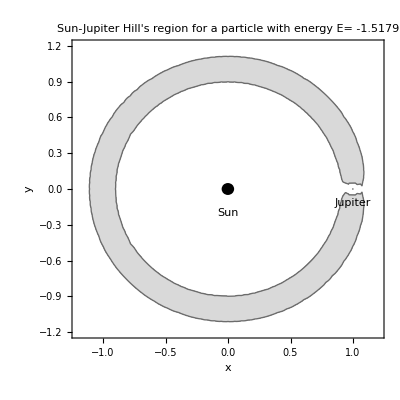

```mathematica
(* Choose an energy level *)
eJS = -1.5179 ;

(* Check if the energy value is enough for the chosen itinerary *)
funcCheckEnergyLevel[ systemId,itinerary , eJS ] 

funcHillRegionsPlot[systemId,eJS,PlotLabel->Style[Framed["Sun-Jupiter Hill's region for a particle with energy E= " <> ToString[eJS]],12,Blue,Background->Lighter[Green]], PlotRange-> {{-1.2,1.2},{-1.2,1.2}}]
```

Step 2 : Computing the Location of the Equilibrium Points

The Lagrange points of the system are : {{0.9328,0},{1.06839,0},{-1.00039,0},{0.499064,0.866025},{0.499064,-0.866025}}

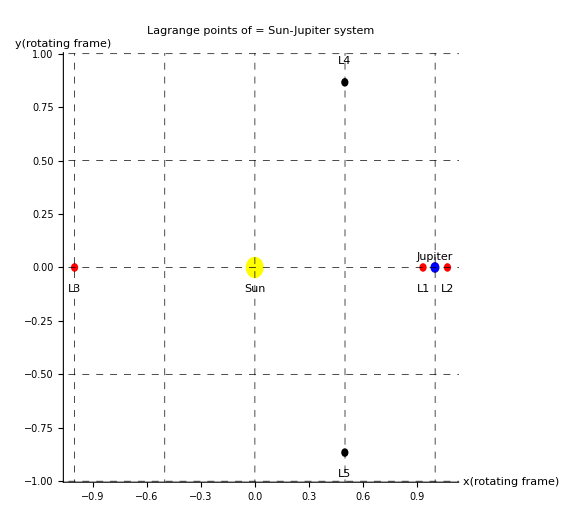

```mathematica
{ L1JS , L2JS , L3JS,L4JS,L5JS } = funcLagrangePoints[μJS] ;
Print["The Lagrange points of the system are : " , { L1JS , L2JS , L3JS,L4JS,L5JS } ]

funcLagrangePointsPlot[systemId]
```

Step 3 : Compute the L1 and L2 Periodic Orbits Using Differential Correction and Numerical Continuation

### Initial conditions for L1 and L2 periodic orbits in the linearized system

```mathematica
(* Initial conditions for L1 periodic orbit in linearized system *)
linL1Ax = 7*10^ -3 ;
linL1poX0=funcInCondLyapOrbit[μJS,"L1",linL1Ax];

(* Check if the energy is near the desired value eJS *)
enL1=funcOrbitEnergy[μJS,linL1poX0+{L1JS[[1]],0,0,0}] ;
enL1- eJS;

funcHillRegionsPlot[systemId,enL1,PlotRange-> {{-1.5,1.5},{-1.5,1.5}}] ;

(************************************************************************)
(* Initial conditions for L2 periodic orbit in linearized system *)
linL2Ax = 7*10^ -3 ;
linL2poX0=funcInCondLyapOrbit[μJS,"L2",linL2Ax ];

(* check if the energy is near the desired value eJS *)
enL2=funcOrbitEnergy[μJS,linL2poX0+{L2JS[[1]],0,0,0}] ;
enL2 - eJS;

funcHillRegionsPlot[systemId,enL2,PlotRange-> {{-1.5,1.5},{-1.5,1.5}}] ;
```

### L1 periodic orbit in linearized system

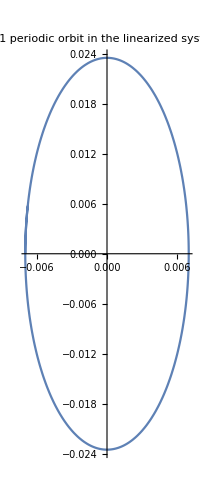

```mathematica
stateRespL1po=funcLinSysStateResponse[systemId,"L1",linL1poX0,0,4];

Plot[Evaluate[stateRespL1po],{t,0,4},PlotLabels-> {"x[t]","y[t]","xDot[t]","yDot[t]"}] ;

ParametricPlot[ Evaluate[ stateRespL1po[[1;;2]] ] , {t,0,3},
PlotLabel->Style[Framed["L1 periodic orbit in the linearized system"],16,Green,Background->Lighter[Gray]]
 ]
```

### L2 periodic orbit in linearized system

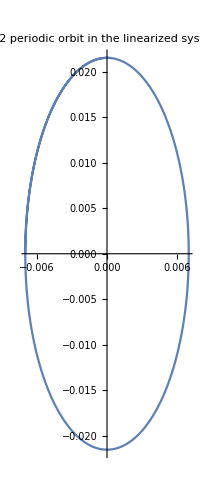

```mathematica
stateRespL2po=funcLinSysStateResponse[systemId,"L2",linL2poX0,0,4];

Plot[Evaluate[stateRespL2po],{t,0,4},PlotLabels-> {"x[t]","y[t]","xDot[t]","yDot[t]"}] ;

ParametricPlot[ Evaluate[ stateRespL2po[[1;;2]] ] , {t,0,4},
PlotLabel->Style[Framed["L2 periodic orbit in the linearized system"],16,Green,Background->Lighter[Gray]]
 ]
```

### Differential correction to compute periodic orbit in non linear system

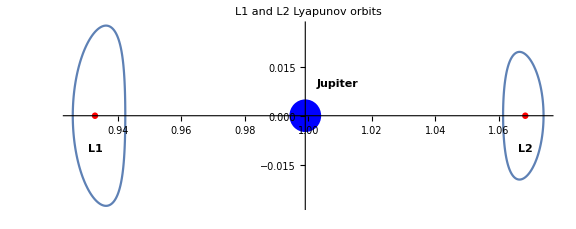

```mathematica
(* N.B After some tries i found that, for L1 periodic orbits, besides Ax=7*10^-3 the differential correction becomes instable and so unusable ;
while for L2 periodic orbits the limit is near *)
L1AxExample=7*10^-3 ;
L2AxExample =7*10^-3 ;
dExample = 10^-8 ;
tfinExample =8;
{t1L1Example,x0L1Example ,x1tL1Example} = funcComputeLyapOrb[μJS,"L1",L1AxExample,tfinExample,dExample] ;
{t1L2Example,x0L2Example ,x1tL2Example} = funcComputeLyapOrb[μJS,"L2",L2AxExample,tfinExample,dExample] ;

Show[{
Graphics[{Blue , Disk[{1-μJS,0},0.005]}],
Graphics[{Text[Style["Jupiter",Medium,Bold,Black],{1-μJS+0.01,0.01}, Background->LightBlue]}],

Graphics[{Red , Disk[L1JS,0.001]}],
Graphics[{Text[Style["L1",Small,Bold,Black],L1JS-{0,0.01}, Background->LightRed]}],
funcNonLinSystemPlot[ μJS,x0L1Example ,0,2*t1L1Example] ,

Graphics[{Red , Disk[L2JS,0.001]}],
Graphics[{Text[Style["L2",Small,Bold,Black],L2JS-{0,0.01}, Background->LightRed]}],
funcNonLinSystemPlot[ μJS,x0L2Example ,0,2*t1L2Example] 
},
AxesOrigin->{1-μJS,0},
Axes->True,
PlotRange-> All,
ImageSize->Large,
PlotLabel->Style[Framed["L1 and L2 Lyapunov orbits"],16,Yellow,Background->Lighter[Blue]]

]
```

### Numerical continuation to compute families of L1 and L2 lyapunov orbits

```mathematica
numberOfL1LyapOrbits =20 ;
lagrPointName = "L1" ;
inAxL1 =7*10^-3 ;
tfin = 8 ;
d = 10^-7 ;

{ L1x0List , L1t1List } = funcGenerateLyapunovOrbitFamily[μJS,"L1" ,inAxL1,tfin,d,numberOfL1LyapOrbits ] ;

numberOfL2LyapOrbits =20 ;
lagrPointName = "L2" ;
inAxL2 =9*10^-3;
tfin = 8 ;
d = 10^-7 ;

{ L2x0List , L2t1List } = funcGenerateLyapunovOrbitFamily[μJS,"L2" ,inAxL2,tfin,d,numberOfL2LyapOrbits ] ;
```

### Pick the Lyapunov orbits with desired energy

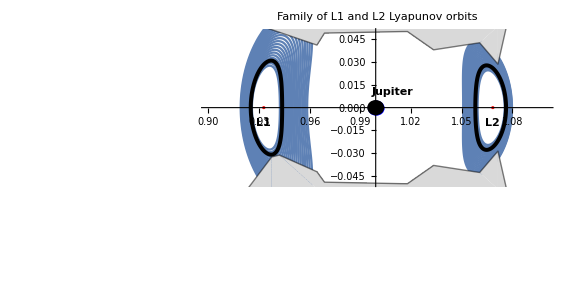

```mathematica
{L1x0,L1t1}=funcFindFirstPossibleX0andt1Values[μJS,eJS,L1x0List,L1t1List,"L1",inAxL1,tfin,d] ;
{L2x0,L2t1}=funcFindFirstPossibleX0andt1Values[μJS,eJS,L2x0List,L2t1List,"L2",inAxL2,tfin,d] ;

Show[{
funcNonLinSystemPlot[μJS, L1x0List[[#]] ,0,2*L1t1List[[#]]] &/@ Range[1,numberOfL1LyapOrbits ,1],
funcNonLinSystemPlot[μJS, L2x0List[[#]] ,0,2*L2t1List[[#]]] &/@ Range[1,numberOfL2LyapOrbits ,1],

funcNonLinSystemPlot[ μJS,L1x0 ,0,2*L1t1 , PlotStyle->  {Black,Thickness[0.005]}],
funcNonLinSystemPlot[μJS, L2x0 ,0,2*L2t1,  PlotStyle->  {Black,Thickness[0.005]}],

Graphics[{Blue , Disk[{1-μJS,0},0.005]}],
Graphics[{Text[Style["Jupiter",Medium,Bold,Black],{1-μJS+0.01,0.01}, Background->LightBlue]}],

Graphics[{Red , Disk[L1JS,0.001]}],
Graphics[{Text[Style["L1",Small,Bold,Black],L1JS-{0,0.01}, Background->LightRed]}],


Graphics[{Red , Disk[L2JS,0.001]}],
Graphics[{Text[Style["L2",Small,Bold,Black],L2JS-{0,0.01}, Background->LightRed]}],

funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L2x0]]

},
PlotRange->{{0.9,1.1},{-0.05,0.05}},
AxesOrigin->{1-μJS,0},
Axes->True,
ImageSize -> Large,
PlotLabel->Style[Framed["Family of L1 and L2 Lyapunov orbits"],16,Yellow,Background->Lighter[Blue]]
]
```

Step 4 : Computation of Invariant Manifolds

### L1 periodic orbit inavariant manifold directions

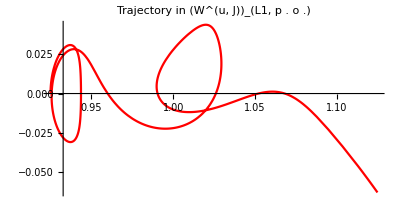

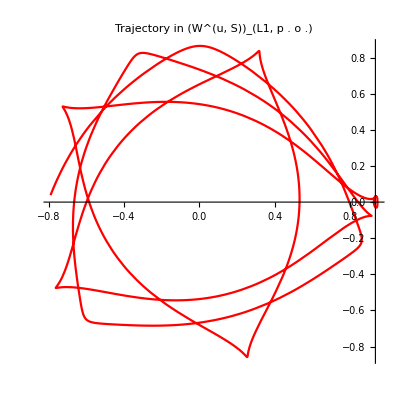

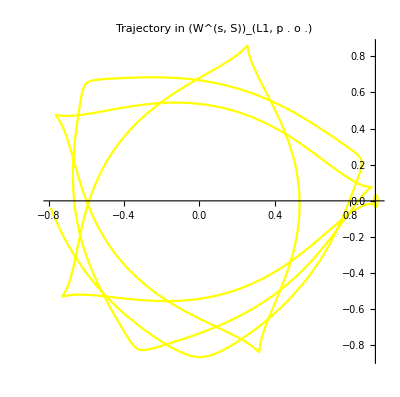

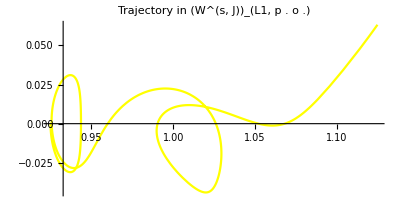

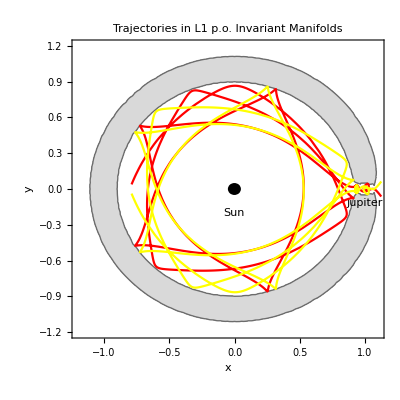

```mathematica
{XstablePlusL1,XstableMinusL1 ,XunstablePlusL1 ,XunstableMinusL1}  = funcComputeInvManifoldDirections[μJS,L1x0,L1t1] ;

Show[{
(* Trajectory in the Jupiter branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[ μJS,XunstablePlusL1 , 0 ,+5*L1t1 , AxesOrigin->L1JS ,  PlotStyle->{Red} ]
},
PlotLabel->Style[Framed["Trajectory in (W^(u, J))_(L1, p . o .)"],16,Red,Background->Lighter[Green]]
] 

Show[{
(* Trajectory in the Sun branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[  μJS,XunstableMinusL1 , 0 ,+30*L1t1 , AxesOrigin->L1JS ,  PlotStyle->{Red}] 
},
PlotLabel->Style[Framed["Trajectory in (W^(u, S))_(L1, p . o .)"],16,Red,Background->Lighter[Green]]
] 

Show[{
(* Trajectory in the Sun branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstablePlusL1 , 0 ,-30*L1t1 , AxesOrigin->L1JS ,PlotStyle->  {Yellow}]
},
PlotLabel->Style[Framed["Trajectory in (W^(s, S))_(L1, p . o .)"],16,Yellow,Background->Lighter[Blue]]
] 

Show[{
(* Trajectory in the Jupiter branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstableMinusL1 , 0 ,-5*L1t1, AxesOrigin->L1JS  ,PlotStyle->  {Yellow} ] 
},
PlotLabel->Style[Framed["Trajectory in (W^(s, J))_(L1, p . o .)"],16,Yellow,Background->Lighter[Blue]]
] 

Show[{
(* Hill region associated to energy level of x0(from which Xstable and Xunstable are generated) *)
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L1x0]] ,

(* Trajectory in the Jupiter branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[ μJS,XunstablePlusL1 , 0 ,+5*L1t1 , AxesOrigin->L1JS ,  PlotStyle->{Red} ],  (* Trajectory in the Sun branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[  μJS,XunstableMinusL1 , 0 ,+30*L1t1 , AxesOrigin->L1JS ,  PlotStyle->{Red}] ,

(* Trajectory in the Sun branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstablePlusL1 , 0 ,-30*L1t1 , AxesOrigin->L1JS ,PlotStyle->  {Yellow}],  (* Trajectory in the Jupiter branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstableMinusL1 , 0 ,-5*L1t1, AxesOrigin->L1JS  ,PlotStyle->  {Yellow} ] 

},
PlotRange->{{-1.2,1.1},{-1.2,1.2}},
PlotLabel->Style[Framed["Trajectories in L1 p.o. Invariant Manifolds"],16,Black,Background->Lighter[Blue]]
]
```

### L2 periodic orbit invariant manifold directions

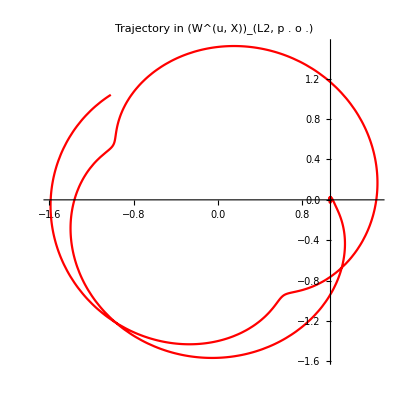

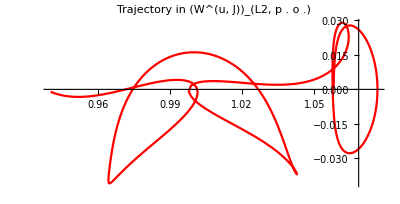

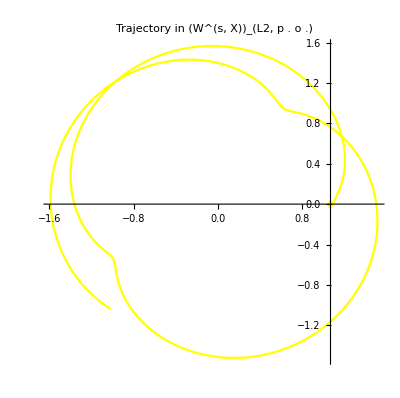

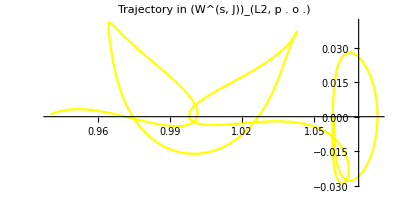

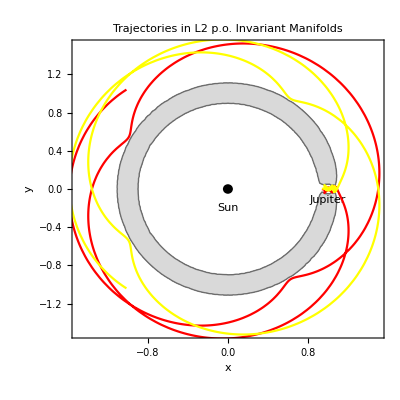

```mathematica
{XstablePlusL2,XstableMinusL2 ,XunstablePlusL2 ,XunstableMinusL2}  = funcComputeInvManifoldDirections[μJS,L2x0,L2t1] ;

Show[{
(* Trajectory in the Exterior branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[ μJS,XunstablePlusL2 , 0 ,+20*L2t1, AxesOrigin->L2JS ,  PlotStyle->{Red} ]
},
PlotLabel->Style[Framed["Trajectory in (W^(u, X))_(L2, p . o .)"],16,Red,Background->Lighter[Green]]
] 

Show[{
(* Trajectory in the Jupiter  branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[  μJS,XunstableMinusL2 , 0 ,+5*L2t1 , AxesOrigin->L2JS ,  PlotStyle->{Red}] 
},
PlotLabel->Style[Framed["Trajectory in (W^(u, J))_(L2, p . o .)"],16,Red,Background->Lighter[Green]]
] 

Show[{
(* Trajectory in the Exterior branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstablePlusL2 , 0 ,-20*L2t1 , AxesOrigin->L2JS ,PlotStyle->  {Yellow}]
},
PlotLabel->Style[Framed["Trajectory in (W^(s, X))_(L2, p . o .)"],16,Yellow,Background->Lighter[Blue]]
] 

Show[{
(* Trajectory in the Jupiter branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstableMinusL2 , 0 ,-5*L2t1, AxesOrigin->L2JS  ,PlotStyle->  {Yellow} ] 
},
PlotLabel->Style[Framed["Trajectory in (W^(s, J))_(L2, p . o .)"],16,Red,Yellow,Background->Lighter[Blue]]
] 
Show[{
(* Hill region associated to energy level of x0(from which Xstable and Xunstable are generated) *)
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L2x0]] ,

(* Trajectory in the Exterior branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[ μJS,XunstablePlusL2 , 0 ,+20*L2t1 , AxesOrigin->L2JS ,  PlotStyle->{Red} ],  (* Trajectory in the Jupiter branch of the Unstable manifold of L1 p.o. *)
funcNonLinSystemPlot[  μJS,XunstableMinusL2 , 0 ,+5*L2t1 , AxesOrigin->L2JS ,  PlotStyle->{Red}] ,

(* Trajectory in the Exterior branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstablePlusL2 , 0 ,-20*L2t1 , AxesOrigin->L2JS ,PlotStyle->  {Yellow}],  (* Trajectory in the Jupiter branch of the Stable manifold of L1 p.o. *)
funcNonLinSystemPlot[μJS, XstableMinusL2 , 0 ,-5*L2t1, AxesOrigin->L2JS  ,PlotStyle->  {Yellow} ] 

},
PlotRange->{{-1.5,1.5},{-1.5,1.5}},
PlotLabel->Style[Framed["Trajectories in L2 p.o. Invariant Manifolds"],16,Black,Background->Lighter[Blue]]
]
```

### L1 p.o. Invariant Manifolds near ℛ_1

```mathematica
granularityL1R1 =80 ;
τPlusL1R1=10*L1t1 ;
τMinusL1R1 =10*L1t1 ;
invManifoldsAndFinPointsAndTimesL1R1= funcComputeLyapunovOrbitInvariantManifolds[μJS,"L1",L1x0, L1t1,τPlusL1R1,τMinusL1R1 , granularityL1R1]  ;

L1InvariantManifoldsL1R1=invManifoldsAndFinPointsAndTimesL1R1[[1]] ;
intersectPointsL1R1 =invManifoldsAndFinPointsAndTimesL1R1[[2]] ;
intersectTimesL1R1 = invManifoldsAndFinPointsAndTimesL1R1[[3]] ;
```

```mathematica
Show[
{
(* Hill region associated to energy level of x0(from which Xstable and Xunstable are generated) *)
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L1x0]] ,

(* Sun branch of the Stable L1 p.o. manifold *)
ParametricPlot[
{L1InvariantManifoldsL1R1[[1,#,1,2]][t],L1InvariantManifoldsL1R1[[1,#,2,2]][t]},
{t,intersectTimesL1R1[[1,#,1]],0},
PlotStyle-> {Yellow}
] &/@ Range[1,Length[intersectTimesL1R1[[1]]] ,1] ,
Graphics[{Text[Style["(W^(s, S))_(L1, p . o .)",Large,Bold,Black] , {0.85,-0.15}  , Background->LightYellow] } ] ,

(* Jupiter branch of the Stable L1 p.o. manifold *)
ParametricPlot[
{L1InvariantManifoldsL1R1[[2,#,1,2]][t],L1InvariantManifoldsL1R1[[2,#,2,2]][t]},
{t,intersectTimesL1R1[[2,#,1]],0},
PlotStyle-> {Yellow}
] &/@ Range[1,Length[intersectTimesL1R1[[2]]] ,1] ,
Graphics[{Text[Style["(W^(s, J))_(L1, p . o .)",Large,Bold,Black] , {0.96,+0.06}  , Background->LightYellow] } ] ,

(* Jupiter branch of the Unstable L1 p.o. manifold *)
ParametricPlot[
{L1InvariantManifoldsL1R1[[3,#,1,2]][t],L1InvariantManifoldsL1R1[[3,#,2,2]][t]},
{t,intersectTimesL1R1[[3,#,1]],0},
PlotStyle-> {Red}
] &/@ Range[1,Length[intersectTimesL1R1[[3]]] ,1] ,
Graphics[{Text[Style["(W^(u, J))_(L1, p . o .)",Large,Bold,Black] , {0.96,-0.06}  , Background->LightRed] } ] ,

(* Sun branch of the Unstable L1 p.o. manifold *)
ParametricPlot[
{L1InvariantManifoldsL1R1[[4,#,1,2]][t],L1InvariantManifoldsL1R1[[4,#,2,2]][t]},
{t,intersectTimesL1R1[[4,#,1]],0},
PlotStyle-> {Red}
] &/@ Range[1,Length[intersectTimesL1R1[[4]]] ,1] ,
Graphics[{Text[Style["(W^(u, S))_(L1, p . o .)",Large,Bold,Black] , {0.85,0.15}  , Background->LightRed] } ] ,

(* periodic orbit *) 
funcNonLinSystemPlot[μJS,L1x0 , 0 ,2*L1t1  ,PlotStyle->  {Black,Thickness[0.005]}]  ,

(* U3 *)
Graphics[{Black,Thickness[0.01],Line[{{1-μJS,0.01},{1-μJS,0.05}}]}] , 

(* U4 *)
Graphics[{Black,Thickness[0.01],Line[{{1-μJS,-0.01},{1-μJS,-0.05}}]}] 

},
 AxesOrigin->L1JS ,
PlotLabel->Style[Framed["Stable and Unstable manifolds of L1 Lyapunov orbit near ℛ_1"],15,Black,Background->Lighter[Yellow]] ,
ImageSize->Large,
PlotRange->{{0.8,1.0},{-0.2,0.2}}

]
```

-Graphics-

### L1 p.o. Invariant Manifolds in the Sun realm

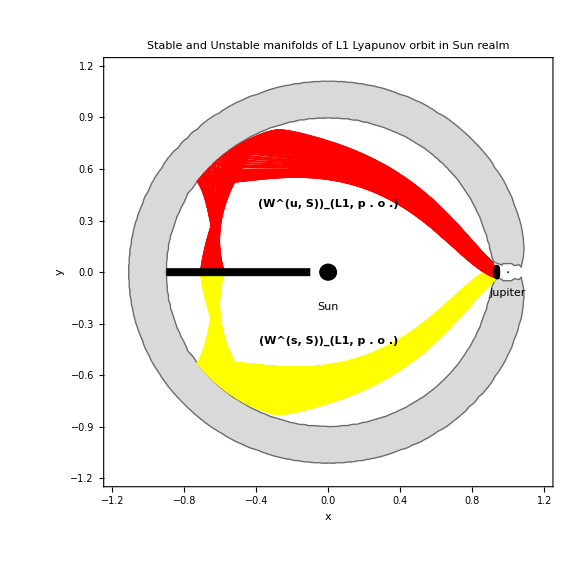

```mathematica
granularityL1Sun =80;
τPlusL1Sun =10*L1t1 ;
τMinusL1Sun =10*L1t1 ;
invManifoldsAndFinPointsAndTimesL1Sun= funcComputeLyapunovOrbitInvariantManifolds[μJS,"L1",L1x0, L1t1,τPlusL1Sun,τMinusL1Sun , granularityL1Sun]  ;

L1InvariantManifoldsL1Sun = invManifoldsAndFinPointsAndTimesL1Sun[[1]] ;
intersectPointsL1Sun= invManifoldsAndFinPointsAndTimesL1Sun[[2]] ;
intersectTimesL1Sun =invManifoldsAndFinPointsAndTimesL1Sun[[3]] ;

Show[
{
(* Hill region associated to energy level of x0(from which Xstable and Xunstable are generated) *)
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L1x0]] ,

(* Sun branch of the Stable L1 p.o. manifold *)
ParametricPlot[
{L1InvariantManifoldsL1Sun[[1,#,1,2]][t],L1InvariantManifoldsL1Sun[[1,#,2,2]][t]},
{t,intersectTimesL1Sun[[1,#,1]],0},
PlotStyle-> {Yellow}
] &/@ Range[1,Length[intersectTimesL1Sun[[1]]] ,1] ,
Graphics[{Text[Style["(W^(s, S))_(L1, p . o .)",Large,Bold,Black] , {0,-0.4}  , Background->LightYellow] } ] ,

(* Sun branch of the Unstable L1 p.o. manifold *)
ParametricPlot[
{L1InvariantManifoldsL1Sun[[4,#,1,2]][t],L1InvariantManifoldsL1Sun[[4,#,2,2]][t]},
{t,intersectTimesL1Sun[[4,#,1]],0},
PlotStyle-> {Red}
] &/@ Range[1,Length[intersectTimesL1Sun[[4]]] ,1] ,
Graphics[{Text[Style["(W^(u, S))_(L1, p . o .)",Large,Bold,Black] , {0,0.4}  , Background->LightRed] } ] ,

(* periodic orbit *) 
funcNonLinSystemPlot[μJS,L1x0 , 0 ,2*L1t1  ,PlotStyle->  {Black,Thickness[0.005]}]  ,

(* U1 *)
Graphics[{Black,Thickness[0.01],Line[{{-0.9,0},{-0.1,0}}]}] 
},

 AxesOrigin->{0,0} ,
PlotLabel->Style[Framed["Stable and Unstable manifolds of L1 Lyapunov orbit in Sun realm"],15,Black,Background->Lighter[Yellow]] ,
ImageSize->Large,
PlotRange->{{-1.2,1.2},{-1.2,1.2}}
]
```

### L2 p.o. Invariant Manifolds near ℛ_2

```mathematica
granularityL2R2 =80 ;
τPlusL2R2 =15*L2t1 ;
τMinusL2R2 =15 *L2t1 ;
invManifoldsAndFinPointsAndTimesL2R2= funcComputeLyapunovOrbitInvariantManifolds[μJS,"L2",L2x0, L2t1,τPlusL2R2,τMinusL2R2 , granularityL2R2]  ;
L2InvariantManifoldsL2R2 = invManifoldsAndFinPointsAndTimesL2R2[[1]];
intersectPointsL2R2= invManifoldsAndFinPointsAndTimesL2R2[[2]];
intersectTimesL2R2= invManifoldsAndFinPointsAndTimesL2R2[[3]];

Show[
{
(* Hill region associated to energy level of x0(from which Xstable and Xunstable are generated) *)
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L2x0]] ,

(* Exterior branch of the Stable L2 p.o. manifold *)
ParametricPlot[
{L2InvariantManifoldsL2R2[[1,#,1,2]][t],L2InvariantManifoldsL2R2[[1,#,2,2]][t]},
{t,intersectTimesL2R2[[1,#,1]],0},
PlotStyle-> {Yellow}
] &/@ Range[1,Length[intersectTimesL2R2[[1]]] ,1] ,
Graphics[{Text[Style["(W^(s, χ))_(L2, p . o .)",Large,Bold,Black] , {1.1,0.08}  , Background->LightYellow] } ] ,

(* Jupiter branch of the Stable L2 p.o. manifold *)
ParametricPlot[
{L2InvariantManifoldsL2R2[[2,#,1,2]][t],L2InvariantManifoldsL2R2[[2,#,2,2]][t]},
{t,intersectTimesL2R2[[2,#,1]],0},
PlotStyle-> {Yellow}
] &/@ Range[1,Length[intersectTimesL2R2[[2]]] ,1] ,
Graphics[{Text[Style["(W^(s, J))_(L2, p . o .)",Large,Bold,Black] , {1.03,-0.06}  , Background->LightYellow] } ] ,

(* Exterior branch of the Unstable L2 p.o. manifold *)
ParametricPlot[
{L2InvariantManifoldsL2R2[[3,#,1,2]][t],L2InvariantManifoldsL2R2[[3,#,2,2]][t]},
{t,intersectTimesL2R2[[3,#,1]],0},
PlotStyle-> {Red}
] &/@ Range[1,Length[intersectTimesL2R2[[3]]] ,1] ,
Graphics[{Text[Style["(W^(u, χ))_(L2, p . o .)",Large,Bold,Black] , {1.1,-0.08}  , Background->LightRed] } ] ,

(* Jupiter branch of the Unstable L2 p.o. manifold *)
ParametricPlot[
{L2InvariantManifoldsL2R2[[4,#,1,2]][t],L2InvariantManifoldsL2R2[[4,#,2,2]][t]},
{t,intersectTimesL2R2[[4,#,1]],0},
PlotStyle-> {Red}
] &/@ Range[1,Length[intersectTimesL2R2[[4]]] ,1] ,
Graphics[{Text[Style["(W^(u, J))_(L2, p . o .)",Large,Bold,Black] , {1.03,+0.06}  , Background->LightRed] } ] ,

(* periodic orbit *) 
funcNonLinSystemPlot[μJS,L2x0 , 0 ,2*L2t1  ,PlotStyle->  {Black,Thickness[0.005]}]  ,

(* U3 *)
Graphics[{Black,Thickness[0.01],Line[{{1-μJS,0.01},{1-μJS,0.05}}]}] , 

(* U2 *)
Graphics[{Black,Thickness[0.01],Line[{{1-μJS,-0.01},{1-μJS,-0.05}}]}] 

},
 AxesOrigin->L2JS ,
PlotLabel->Style[Framed["Stable and Unstable manifolds of L2 Lyapunov orbit near ℛ_2"],15,Black,Background->Lighter[Yellow]] ,
ImageSize->Large,
PlotRange->{{0.98,1.2},{-0.2,0.2}}

]
```

-Graphics-

### L2 p.o. Invariant Manifolds in the Exterior realm

```mathematica
granularityL2X =80 ;
τPlusL2X =10*L2t1 ;
τMinusL2X = 10*L2t1 ;
invManifoldsAndFinPointsAndTimesL2X= funcComputeLyapunovOrbitInvariantManifolds[μJS,"L2",L2x0, L2t1,τPlusL2X,τMinusL2X , granularityL2X]  ;
L2InvariantManifoldsL2X= invManifoldsAndFinPointsAndTimesL2X[[1]];
intersectPointsL2X= invManifoldsAndFinPointsAndTimesL2X[[2]];
intersectTimesL2X= invManifoldsAndFinPointsAndTimesL2X[[3]];

Show[
{
(* Hill region associated to energy level of x0(from which Xstable and Xunstable are generated) *)
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L2x0]] ,

(* Exterior branch of the Stable L2 p.o. manifold *)
ParametricPlot[
{L2InvariantManifoldsL2X[[1,#,1,2]][t],L2InvariantManifoldsL2X[[1,#,2,2]][t]},
{t,intersectTimesL2X[[1,#,1]],0},
PlotStyle-> {Yellow}
] &/@ Range[1,Length[intersectTimesL2X[[1]]] ,1] ,
Graphics[{Text[Style["(W^(s, χ))_(L2, p . o .)",Large,Bold,Black] , {1.1,0.8}  , Background->LightYellow] } ] ,

(* Exterior branch of the Unstable L2 p.o. manifold *)
ParametricPlot[
{L2InvariantManifoldsL2X[[3,#,1,2]][t],L2InvariantManifoldsL2X[[3,#,2,2]][t]},
{t,intersectTimesL2X[[3,#,1]],0},
PlotStyle-> {Red}
] &/@ Range[1,Length[intersectTimesL2X[[3]]] ,1] ,
Graphics[{Text[Style["(W^(u, χ))_(L2, p . o .)",Large,Bold,Black] , {1.1,-0.8}  , Background->LightRed] } ] ,

(* periodic orbit *) 
funcNonLinSystemPlot[μJS,L2x0 , 0 ,2*L2t1  ,PlotStyle->  {Black,Thickness[0.005]}]  ,

(* U4 *)
Graphics[{Black,Thickness[0.01],Line[{{-1.3,0},{-2.3,0}}]}] 
},

 AxesOrigin->{0,0},
PlotLabel->Style[Framed["Stable and Unstable manifolds of L2 Lyapunov orbit in the Exterior realm"],15,Black,Background->Lighter[Yellow]] ,
ImageSize->Large,
PlotRange->{{-2,2},{-2,2}}
]
```

-Graphics-

Step 5 : Take a Poincaré Surface of Section of the Globalized Stable and Unstable Manifolds

### U1 first intersections of (W^(u,S))_(L1,p.o.) and (W^(s,S))_(L1,p.o.)

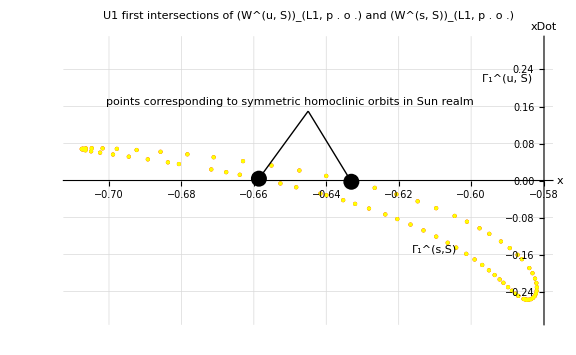

```mathematica
TjS=L1InvariantManifoldsL1Sun[[4]] ;
xjS = TjS[[All,1]][[All,2]] ;

xDotjS = TjS[[All,3]][[All,2]] ;
xIntjS=xjS[[#]][intersectTimesL1Sun[[4,#,1]]]&/@ Range[1,Length[intersectTimesL1Sun[[4]]]]  ;

TSj=L1InvariantManifoldsL1Sun[[1]] ;
xSj= TSj[[All,1]][[All,2]] ;
xDotSj = TSj[[All,3]][[All,2]] ;

xIntSj=xSj[[#]][intersectTimesL1Sun[[1,#,1]]]&/@ Range[1,Length[intersectTimesL1Sun[[1]]]]  ;


xDotIntSj=xDotSj[[#]][intersectTimesL1Sun[[1,#,1]]]&/@ Range[1,Length[intersectTimesL1Sun[[1]]]]  ;

pointsSj = {xIntSj[[#]],xDotIntSj[[#]] } &/@ Range[1,Length[intersectTimesL1Sun[[1]]]] ;

intHomXXdot=MinimalBy[pointsSj,Abs[#[[2]]]& , 2] ;
intHomoPos=Flatten[Position[pointsSj,intHomXXdot[[#]]]&/@{1,2} ] ;

interiorHomoclinicPoints={ 
TSj[[intHomoPos[[1]]]][[#,2]][intersectTimesL1Sun[[1,intHomoPos[[1]] ,1]]]&/@Range[1,4] ,
TSj[[intHomoPos[[2]]]][[#,2]][intersectTimesL1Sun[[1,intHomoPos[[2]] ,1]]]&/@Range[1,4]
} ;

U1PoincareCuts =
{
ListPlot[ pointsSj, PlotStyle-> {Red,PointSize[Medium]}],
Graphics[{Text[Style[" Γ_1^(u, S)  ",Medium,Italic,Black] , {-0.59,0.22}  , Background->Red] } ],
ListPlot[ pointsSj, PlotStyle->{Yellow,PointSize[Medium]}] ,
Graphics[{Text[Style[" Γ_1^(s,S) ",Medium,Italic,Black] , {-0.61,-0.15}  , Background->Yellow] } ],
Graphics[{Black,PointSize-> 0.02,Point[intHomXXdot[[#]]]&/@{1,2}}],

Graphics[{Black,Arrow[{{-0.645,0.15} ,intHomXXdot[[1]]}]}],
Graphics[{Black,Arrow[{{-0.645,0.15} ,intHomXXdot[[2]]}]}],
Graphics[{Text[Style["points corresponding to symmetric homoclinic orbits in Sun realm",Medium,Italic,Black] , {-0.65,0.17}  , Background->Green] } ]
} ;

Show[
U1PoincareCuts,
AxesLabel-> {"x","xDot"},
GridLines->Automatic,GridLinesStyle->Directive[Lighter[Black],Dotted],
PlotLabel->Style[Framed[ "U1 first intersections of (W^(u, S))_(L1, p . o .) and (W^(s, S))_(L1, p . o .)"],15,Black,Background->Lighter[Brown]] ,
PlotRange-> {{-0.71,-0.58},{-0.3,0.3}} , 
ImageSize-> Large
]
```

### Transversal symmetric Homoclinic orbit in Sun realm

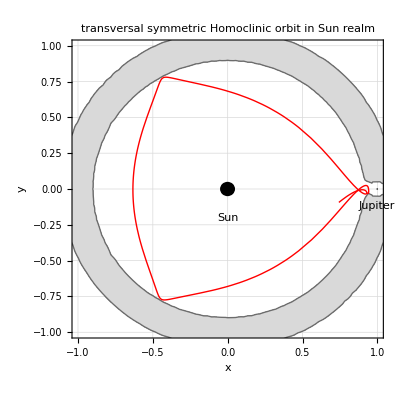

```mathematica
Show[{
funcHillRegionsPlot[systemId,funcOrbitEnergy[μJS,L1x0]] ,
funcNonLinSystemPlot[ μJS,interiorHomoclinicPoints[[1]] , 0,-8,PlotStyle->{ Red , Thick }],
funcNonLinSystemPlot[ μJS,interiorHomoclinicPoints[[1]] , 0, 8,PlotStyle->{ Red , Thick }]
},
AxesOrigin-> {0,0} ,
GridLines->Automatic,GridLinesStyle->Directive[Lighter[Black],Dotted],
PlotLabel->Style[Framed[ "transversal symmetric Homoclinic orbit in Sun realm"],15,Black,Background->Lighter[Green]] ,
PlotRange-> {{-1,1},{-1,1}}
]
```

### U2 first intersections of (W^(u,J))_(L1,p.o.) and (W^(s,J))_(L2,p.o.)

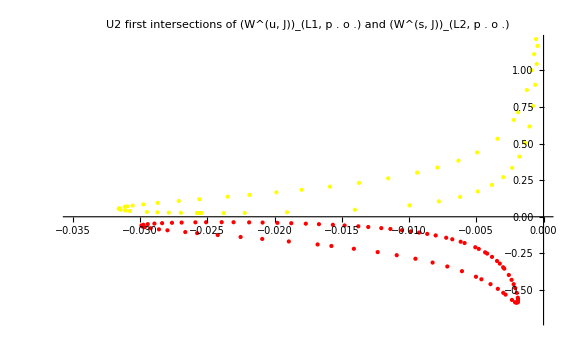

```mathematica
TJx=L1InvariantManifoldsL1R1[[3]] ;
yJx = TJx[[All,2]][[All,2]] ;
yDotJx = TJx[[All,4]][[All,2]] ;

yIntJx=yJx[[#]][intersectTimesL1R1[[3,#,1]]]&/@ Range[1,Length[intersectTimesL1R1[[3]]]]  ;


yDotIntJx=yDotJx[[#]][intersectTimesL1R1[[3,#,1]]]&/@ Range[1,Length[intersectTimesL1R1[[3]]]]  ;


pointsJx = {yIntJx[[#]],yDotIntJx[[#]] } &/@ Range[1,Length[intersectTimesL1R1[[3]]]] ;

TsJ=L2InvariantManifoldsL2R2[[2]] ;
ysJ = TsJ[[All,2]][[All,2]]  ;
yDotsJ = TsJ[[All,4]][[All,2]]  ;

yIntsJ=ysJ[[#]][intersectTimesL2R2[[2,#,1]]]&/@ Range[1,Length[intersectTimesL2R2[[2]]]]  ;


yDotIntsJ=yDotsJ[[#]][intersectTimesL2R2[[2,#,1]]]&/@ Range[1,Length[intersectTimesL2R2[[2]]]]  ;


pointssJ = {yIntsJ[[#]],yDotIntsJ[[#]] } &/@ Range[1,Length[intersectTimesL2R2[[2]]]] ;

U2PoincareCuts =
{
ListPlot[ pointsJx, PlotStyle-> {Yellow,PointSize[Medium]}],
ListPlot[ pointssJ, PlotStyle->{Red,PointSize[Medium]}]
} ;

Show[
U2PoincareCuts,
PlotLabel-> "U2 first intersections of (W^(u, J))_(L1, p . o .) and (W^(s, J))_(L2, p . o .)" , 
PlotRange-> {{-0.035,0},{-0.7,1.2}} , 
ImageSize-> Large
]
```

### U3 first intersections of (W^(s,J))_(L1,p.o.) and (W^(u,J))_(L2,p.o.)

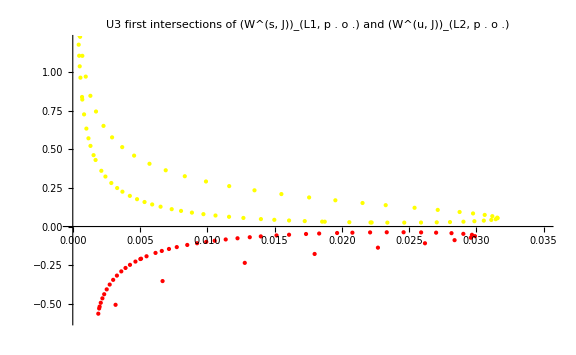

```mathematica
TJs=L1InvariantManifoldsL1R1[[2]] ;
yJs = TJs[[All,2]][[All,2]]  ;
yDotJs = TJs[[All,4]] [[All,2]] ;

yIntJs=yJs[[#]][intersectTimesL1R1[[2,#,1]]]&/@ Range[1,Length[intersectTimesL1R1[[2]]]] ;

yDotIntJs=yDotJs[[#]][intersectTimesL1R1[[2,#,1]]]&/@ Range[1,Length[intersectTimesL1R1[[2]]]] ;
pointsJs = {yIntJs[[#]],yDotIntJs[[#]] } &/@ Range[1,Length[intersectTimesL1R1[[2]]]] ;

TxJ=L2InvariantManifoldsL2R2[[4]] ;
yxJ = TxJ[[All,2]][[All,2]]  ;
yDotxJ = TxJ[[All,4]][[All,2]]  ;

yIntxJ=yxJ[[#]][intersectTimesL2R2[[4,#,1]]]&/@ Range[1,Length[intersectTimesL2R2[[4]]]] ;

yDotIntxJ=yDotxJ[[#]][intersectTimesL2R2[[4,#,1]]]&/@ Range[1,Length[intersectTimesL2R2[[4]]]] ;
pointsxJ = {yIntxJ[[#]],yDotIntxJ[[#]] } &/@ Range[1,Length[intersectTimesL2R2[[4]]]] ;

U3PoincareCuts = {
ListPlot[ pointsJs ,  PlotStyle-> {Yellow,PointSize[Medium]}],
ListPlot[ pointsxJ , PlotStyle-> {Red,PointSize[Medium]}]
} ;

Show[
U3PoincareCuts ,
PlotLabel-> "U3 first intersections of (W^(s, J))_(L1, p . o .) and (W^(u, J))_(L2, p . o .) " ,
PlotRange-> {{0,0.035},{-0.6,1.2}} , 
ImageSize-> Large
]
```

### U4 first intersections of (W^(u,X))_(L2,p.o.) and (W^(s,X))_(L2,p.o.)

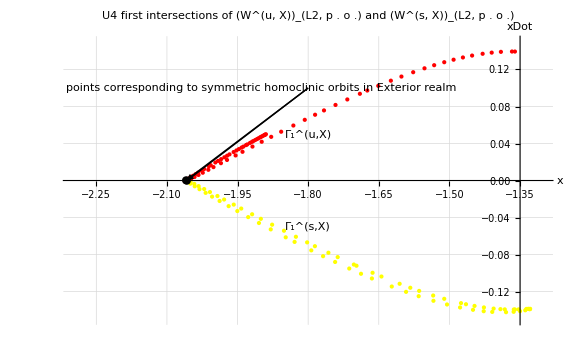

```mathematica
TjX=L2InvariantManifoldsL2X[[3]] ;
xjX = TjX[[All,1]][[All,2]] ;
xDotjX = TjX[[All,3]] [[All,2]];

xIntjX=xjX[[#]][intersectTimesL2X[[3,#,1]]]&/@ Range[1,Length[intersectTimesL2X[[3]]]]  ;


xDotIntjX=xDotjX[[#]][intersectTimesL2X[[3,#,1]]]&/@ Range[1,Length[intersectTimesL2X[[3]]]]  ;


pointsjX= {xIntjX[[#]],xDotIntjX[[#]] } &/@ Range[1,Length[intersectTimesL2X[[3]]]]  ;

TXj=L2InvariantManifoldsL2X[[1]] ;
xXj= TXj[[All,1]][[All,2]];
xDotXj = TXj[[All,3]][[All,2]] ;

xIntXj=xXj[[#]][intersectTimesL2X[[1,#,1]]]&/@ Range[1,Length[intersectTimesL2X[[1]]]]  ;

xDotIntXj=xDotXj[[#]][intersectTimesL2X[[1,#,1]]]&/@ Range[1,Length[intersectTimesL2X[[1]]]]  ;

pointsXj= {xIntXj[[#]],xDotIntXj[[#]] } &/@ Range[1,Length[intersectTimesL2X[[1]]]] ;

extHomXXdot=MinimalBy[pointsjX,Abs[#[[2]]]& , 2] ;
extHomoPos=Flatten[Position[pointsjX,extHomXXdot[[#]]]&/@{1,2} ] ;

exteriorHomoclinicPoints={ 
TjX[[extHomoPos[[1]]]][[#,2]][intersectTimesL2X[[3,extHomoPos[[1]]]]]&/@Range[1,4] ,
TjX[[extHomoPos[[2]]]][[#,2]][intersectTimesL2X[[3,extHomoPos[[2]]]]]&/@Range[1,4]
}  ;

U4PoincareCuts = {
ListPlot[ pointsjX, PlotStyle-> {Red,PointSize[Medium]}],
Graphics[{Text[Style[" Γ_1^(u,X)",Medium,Italic,Black] , {-1.8,0.05}  , Background->Red] } ],

ListPlot[ pointsXj, PlotStyle->{Yellow,PointSize[Medium]}] ,
Graphics[{Text[Style[" Γ_1^(s,X)",Medium,Italic,Black] , {-1.8,-0.05}  , Background->Yellow] } ],
Graphics[{Black,PointSize-> 0.01,Point[extHomXXdot[[#]]]&/@{1,2}}],

Graphics[{Black,Arrow[{{-1.8,0.1} ,extHomXXdot[[1]]}]}],
Graphics[{Black,Arrow[{{-1.8,0.1} ,extHomXXdot[[2]]}]}],
Graphics[{Text[Style["points corresponding to symmetric homoclinic orbits in Exterior realm",Medium,Italic,Black] , {-1.9,0.1}  , Background->Green] } ]
} ;

Show[
U4PoincareCuts,
AxesLabel-> {"x","xDot"},
GridLines->Automatic,GridLinesStyle->Directive[Lighter[Black],Dotted],
PlotLabel->Style[Framed["U4 first intersections of (W^(u, X))_(L2, p . o .) and (W^(s, X))_(L2, p . o .)"],15,Black,Background->Lighter[Brown]] ,
PlotRange-> {{-2.3,-1.3},{-0.15,0.15}} , 
(*
PlotRange-> {{-2.07,-2.13},{-0.05,0.05}} , 
*)
ImageSize-> Large
]
```